```mathematica
FileNameForTupleBis[primes_] := Module[{fileName, temp, sep, pPos},
    sep = "\\";
    temp = "d:\\triangle\\DataSrc";
    For[pPos = 1, pPos <= Length[primes], pPos++,
      temp = StringJoin[temp, sep, ToString[primes[[pPos]]]];
      ];
    If [Not[DirectoryQ[temp]],
   CreateDirectory[temp]
   ];
    temp = StringJoin[temp, "\\SolutionsBis.txt"];
    fileName = temp;
    Return[fileName]
   ]
```

```mathematica
CalcGoodForTuple2[tuple_, start_,end_] := Module[{sorted,fileName, file, current, index, dummy, range=1000, continue, distance,l=Length[tuple],zero=0,primeIndex=1, attempt=1},
(* always make sure the tuple is sorted *)
sorted = Sort[tuple];
fileName = FileNameForTupleBis[sorted];
index = 0;
current = 0;

(* read any existing good values - actually read the last one and store it in the current variable.   Also increment the index variable *)
If [FileExistsQ[fileName],
Monitor[
continue = True;
file = OpenRead[fileName];
While[continue,
dummy = ReadList[file, Number, range];
index += Length[dummy];
If [Length[dummy] ≠ 0, current = Last[dummy]];
If [current ≥end, continue=False];
If[Length[dummy] ≠ range, continue = False];
];
Close[file];
current +=1;
,
"Reading existing " <> fileName <> " value " <> ToString[index]
]
];
current=Max[start,current];
(* now calculate good values and append them to the file for as long as the bound is not reached *)
(* If the process is aborted, the file is closed *)
file = OpenAppend[fileName, PageWidth->40000];
CheckAbort[
Monitor[
While[current<end,
distance = Distance[current, sorted[[primeIndex]]];
current += distance;
If [distance == 0,
zero+=1;
(*Print[{current,primeIndex,zero,distance}];*)
If[zero==l,
index +=1;
zero=0;
Write[file,current];
current+=1,
attempt=0
],
zero=0
];
attempt+=1;
primeIndex=Mod[primeIndex,l]+1;
]
,
"Calculating good values " <> fileName <> ". " <> ToString[index] <> " found."<> "- " <> ToString[N[Log[10,current],50]] <> "  " <> ToString[attempt]
];
Close[file];
,
Print["Aborted at value : " <> ToString[index] ];
Close[file];
Abort[];
];
]
```

```mathematica
CalcGoodForTuple2[{3,5,7,11},100000,10^2000000]
```

```mathematica
CloseStreams[]
```

```mathematica
Clear[ddd]
```

```mathematica
Timing[ddd=CalcGoodForTuple2[{3,5,7,11},0,10^10000]]
```

{1270.75,{0,«189205»}}

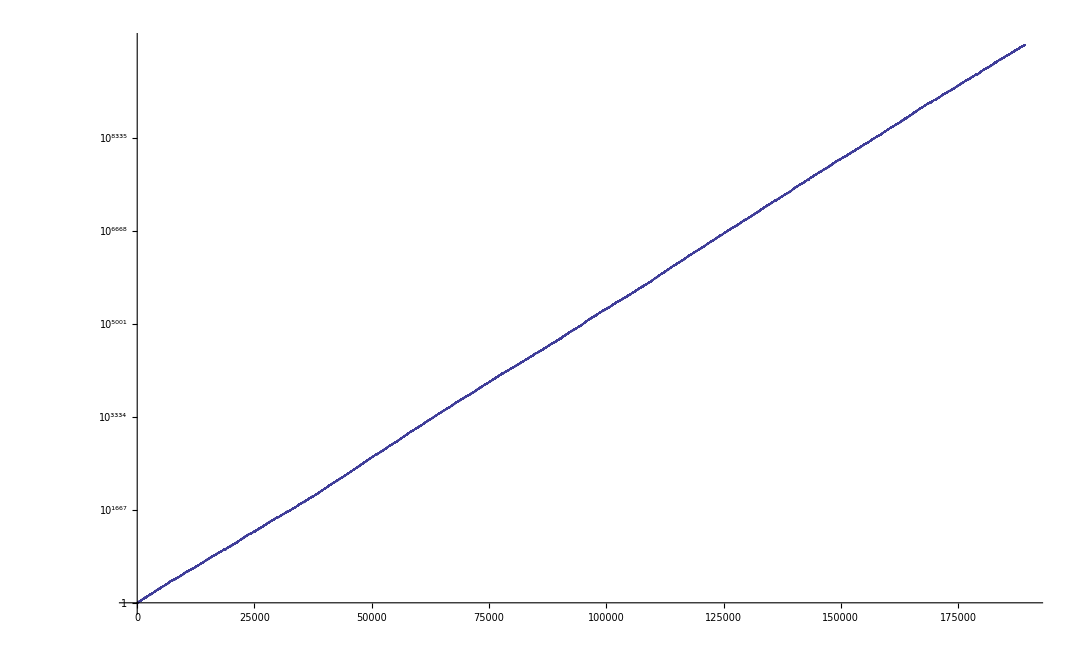

```mathematica
ListLogPlot[ddd,Joined->True]
```

```mathematica
NumberForm[N[Log[10,2^1000]],20]
```

301.0299956639812

```mathematica
ToString[N[Log[10,2^10000]]]
```

3010.3

```mathematica
CalcGoodForTuple2[{7,11,13,17},10^10000,10^200000]
```

Aborted at value : 140

$Aborted

```mathematica
Calculating good values d:\triangle\DataSrc\7\11\13\17\SolutionsBis.txt.140 found.-2093.8052866032022598929414969532820083014007059442 176266
```

```mathematica
Calculating good values d:\triangle\DataSrc\7\11\13\17\SolutionsBis.txt.140 found.-16085.964445385040473162295597944003378126629503872 3812265
```

```mathematica
CalcGoodForTuple2[tuple_, start_,end_] := Module[{sorted,fileName, file, current,lowest,logCurrent, index, dummy, range=1000, continue, distance,l=Length[tuple],zero=0,primeIndex=1, attempt=1},
(* always make sure the tuple is sorted *)
sorted = Sort[tuple];
fileName = FileNameForTupleBis[sorted];
index = 0;
current = 0;
lowest = Infinity;

(* read any existing good values - actually read the last one and store it in the current variable.   Also increment the index variable *)
If [FileExistsQ[fileName],
Monitor[
continue = True;
file = OpenRead[fileName];
While[continue,
dummy = ReadList[file, Number, range];
index += Length[dummy];
If [Length[dummy] ≠ 0, current = Last[dummy]];
If [current ≥end, continue=False];
If[Length[dummy] ≠ range, continue = False];
];
Close[file];
current +=1;
,
"Reading existing " <> fileName <> " value " <> ToString[index]
]
];
current=Max[start,current];
(* now calculate good values and append them to the file for as long as the bound is not reached *)
(* If the process is aborted, the file is closed *)

file = OpenAppend[fileName, PageWidth->40000];
CheckAbort[
Monitor[
While[current<end,
distance = Distance[current, sorted[[primeIndex]]];
logCurrent=N[Log[10,distance]];
If[logCurrent<lowest,lowest=logCurrent];
current += distance;
If [distance == 0,
zero+=1;
(*Print[{current,primeIndex,zero,distance}];*)
If[zero==l,
index +=1;
zero=0;
Write[file,current];
current+=1,
attempt=0,
lowest = Infinity
],
zero=0
];
attempt+=1;
primeIndex=Mod[primeIndex,l]+1;
]
,
"Calculating good values " <> fileName <> ". " <> ToString[index] <> " found."<> "- " <> ToString[N[Log[10,current],50]] <> "  " <> ToString[attempt]<> "  " <> ToString[logCurrent]<> "  (" <> ToString[lowest] <> ")"
];
Close[file];
,
Print["Aborted at value : " <> ToString[current] ];
Close[file];
];
]
```

```mathematica
Length[GoodForTuple[{7,11,13,19}]]
```

7546

```mathematica
Timing[ CalcGoodForTuple2[{7,11,13,19},0,10^20000]]
```

Aborted at value : 2370

$Aborted

```mathematica
CloseStreams[]
```

```mathematica
vv=CalcGoodForTuple2[{3,31,43,173,229},9470571181712199978268376707994551133489965446732670696653473369761793404897029400959301735942331685063044894797184741289848713270196865805609546708536545069619827825338741764526775466982498955861002834279632720169027053041786170580382715119090731472577205252962384303998943204644404179209785446868219525290605828839537113844376169487259799471238544571372200537245643308920459626986161069304707512212290810332994242988966721977199738708881755594640035720548316572220826482343187549252760601120344140943049059955091449295633488135006855494511598931670685831486856439108851702626770109758441410153004975861477481573918879733384869230516252827769067590758948123527312677309791768727222173571486724040673803532977900140683698832184600161534732000249237152046029362785176127843112993503582513965163699137007651441658770054883163735786383108203406312900851136601959582575223408715869745866663263283355644074928982145865475443828019245056304252129619164058199605785013329572450193854682410928319200769674944769217107367670070015542120218997696517920449751119106961292385632425662157854875056976692555303375976313998128025768120708828913586412890377845397591974232656434306117936102184139228853533302799253226410827318420646647958572717373479339109215982429250654158488039072413677844961960278886720582905534726788315257807172973350265372215829077384938678971377612959376063481144777461019357278778952229544275088087681496188798405112203283246314883272669435864554976391924693013968224821542798705913258959801081665873280254088106689182112293180425838932689224965168991520632559262694586689642432633067292690034170062448768713101664760486530394514958021564832076876510358191373920097727767936446891247955488940080518056514839157632708179091000319455684746688615159679337838550926977984767058518632764401263211882005367524175526583931379957731164849954770408444864742961151581119736542825723109331065208189341460472512437658840934806948185327254509956552094834731503255294288134479686408767659218528500302699021870604989971958535405358851088997820039202159084497932627864425582574080949349379564663391270687511269378419707341505661224604013869794861635888965698907854351209963233211785601959317844159541384647781154497816407276816277509836358140589928365803082409670427611077058845923916531199924983849263942977422698754374947157820500920926471727915091258220920602519345042363602270757216569793782865605303932194245912070342620632058519614779485256419785450844473887056424498349223070339122161135761480111648809453510417374323793625530591635612324359608290493458339778764988361086689963356329605259448606751809044892394712186082692521786160536367951493635140945215335194124049709749993491073657562909931880030677526813409931017964103078580448620271319113057223507879378695769506936129346570159814664399320548579306246909950931377593071115628184618211491725675335743089213541074161018146653863295214596641208510857990248723720760588177247636740850704813674844992622395617848431402894353019437737572364398843108886490829984770323815136735216714019821890841172863940316385372823297078893263042074023290504170536536607999924506146364355004726551933817695186729213936478163131277922562551061009437491022607476701246596640668064067229986850651504985920682902286787693720290707871888470292035812558191752372585117870485486244216665893769224631698876161570778917585720516570787245626881313438541628932263371042584228977295342860033578731059757822345395061862740942972335567756142945764132623421170793338169929614818880751866850511209577373247604326144286900786160062322629139621241588531381349128930069053176347031603922055002482901468914299601922966766203593867253806904707888030028661139699977498160360375570383192932886876376625061121979371570270517800659415198627163471982924158218979917314835903208189332284718036199645920775099145766490865206198999814223395149284812063148165475022627451641581559493970029209164943865614566949098861998565484826849732630287576346089527691865729725395047955226786685177159795941127090827187501033205924663505465881084568796739855045088641612076696448029083552330686581932355102382345132450333079026671795066927714598940630788618628544085676085388504284792147399933835047720123733478160229600228386607008486155937317349350802678002974443079196150989613437151343692384350368637544189021826292058055411389446467586607091876981169379722049211115792613699607203617904907586451676313047599072958428882845558458299831775347532705647416213490772023734501210957300260440154321396460306065538275055303956724847129894849928190207623706506868175890905851758866494415651012054114388958940542211039207278440361878165201134609857421535323780917264630029559105238707967762137693095374091321560348714575194803376429087381355100435828076099297821823551175442730352110425673850733579240830645418749192860091037991422049293380672324180257891702312527791414778973874275974064815310834224823333017699118661923397738227245556664597992135763073611414628134246584753053915966426252288349581476673024903547638806342523345712675750175829534997592249351020409588606082379726099621971457482412604584063822996488766530586386249962527160413365423552054361389979165485636848058177112871865897626100231950624328481783166910138296971722645995799968366112974024514358545622238365462681344433374133991936998478495503306718228421750675628240854425573813188243327996815915063827554619194863263594488473383405905485924008420403094007469684418813702926004819084941515260055839802323344225901985242297010214052123276276890388594525272371903895700894127943517977751769121374121828534495204681106658547867063481580994380259196106360342964197048399536792267585851062939945669130500950257105284448652700510972458945633102223305989069711043371774110289051647157136275460084355978446446887599627806815935010575850902217451396578594989268422670231217828282377818233056267301605195135404616085510442491095095867337154071556445472775415330603427426867739160077654713662143764433814358922198059126363878009359264494537177433625987906224701464847576654469988919802700560750967278965522725829414478582357100639074832018055426032746060353262971931200085871117103971933255110266041175574476166528438444680609493961749959815633824978383608208398865012729734128319612077021378319495318888942047442508224310081852145234913650298982197759371074735906757307493461295699683881212279336348444695419168654369992823283769690105432650760548495954556336509903688119903654334661688807567776480626211589324683064664801821011846355712287102510676153163811745888096647425488485962988842561384870302976843657301279879304123631743040689113761840967158272754763520409239523098543784560735106913806967133994045935661428701099677911649601776011183689563243169801348106783125029136827574205179002868668069095151349983077857938916088321478677365013022195215960754402627433601039202032648492468460494085046995702792475993937293210639336484358915034187016995760253345818550104355594441402177485004804904258173325443332318517250405693944685357805981231180339981768455849303132619599283118903422406837570969127456477624178373959703939459848583599305859266368554055178423612494773113446330282426386323647262545348393476854326694419372612068525435733947273641355592451006131756939282347376054941139022323856814920738576689045761022102296558759150958022401787241098110553125007296628250134640657955255558919579040406580436781190332254786597026616685496730921282579185801537617649069227307284666535874927765349128417322974931181094679483915962661244965331979053920523854063326934967765051035038841179898047596708952415696597355098491937385052267234097271869052596062677394233984735470513217362786698176514697998704229672813679494402574852336556512608807236394065108971950817110051401685619950904006717694244357341878533040194584366041687781682572296738893883856807597521542754098731407646969496374927743560796404742645033716573273647729406224709513282650071709585979756419850446216664180119866001625797663985172015144148260699717240057313870627350727650628838904535403051327033008704123190543231842335032831944563623116510533411915326271329568382633856282324186445265471537453838921258658298342042029724796191115229931591951929211837915274967777879213044308448401264340297855799621681250002158745715922141302376863334707607755402681545896106728400865880071943933974782499279334138916221001448911732026143450824778795262914157197563488954274530076163721355576118789481119941892302934026484626258714388861860085195912767692276667316966003334005148160188035627851896444766694718765798545475940771996559797589308131374123590438782040962201517281421527938444739939374517322229626624032085776094209235924334182935293167195108420882075687017088307700789042804119156748498661535511204329848747551639344699020124941820738737724996337359361344032082873744889036317680141827008373553695835303144886660558088222007379846592689804099337883462708584300066673465275829635965036960912567886670471178633216143576191477727225559371279793797050131224413657101829492977575347568122850392447373899899563409540396164213849947502027719499345915441280119556882771053390862167168219148945872972019796021195130221105425632494645891818149436885725931305904881727588403623336099444550434719339081800602181214665593169575479156694085298391852032444696620237801415348964459503659907727645146987810839110352554096184886101720382045971532275012704221262016516207999563227590019686973812685513563579315856581129303330036494852131083467848289024167543931759894200691142268052151508411111741227206785606428321908609393767679745330108187169128186944758486159067591244218530567125772511901237080851208094862874160905512848682329434138634547508416601564476152861920469386834700811928799195817886109079561552160943146330318251140646518261435618696049777113736934512647116565600478298957841588231285788230658280945521929709130970997974796908606814336876177565428382467432389935458659026536060858085346798296928088122935566594291539423828047670553760679870830535280487890613627401132093378131386147092579030257217096965216743367930680226374388408378270886432773837794340784981854576027427530070937995905470063183848022528571882298605850989749510930457966215985717686514879881337405686757544657095743297862416709108302098288803914810241879921084204656276341765962237486421486895141792977764019651728724059884104669780886507015346710636579792459040524086154172039369815839166293088892898884852635259671691290962381813874589241296375967170477134655095476162976687537064416189837133762159890299939517895301124967499662059236109971906245309411274562110470360568476432559180185079098994755090435491665263514438122883075714249846005110849234676001694987423781333530528737282152465045830489445332377206296959395314666308702551265637603719036635409933406308226146625889156654523798385188177353450746214492835048084244622620712371927859045274757331526102666298144916767299762954818162429066270198961997618774068638466723687426503175611788453014191768730853945150260042863478958666714536311673371320432950654734428763891221688651373692694131724660885781085922681567599219034944216088271179162563301582011693374121494030032395766277811971432979073388364980032997993379253859118736992847795520559914722196099658310110283660391538939923292951461049237700292789933860803044087185121821183877351976074150334765606674679813403497743083296786283079072883031200614355113682166219386294173202362372601146502425305890521490024,10^20000]
```

Aborted at value :

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-23895.343716916124583772456664760927287951275264801 1159011 (14487.5)-14956.3-(17167.9)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-23895.343716916124583772456664760927287951275264801 655535 (14646.8)-16149.5-(17167.9)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-23895.343716916124583772456664760927287951275264801 207724 (14646.8)-15894.9-(15913.3)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-23895.343716916124583772456664760927287951275264801 114710 (14646.8)-14925.3-(15674.7)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-23895.343716916124583772456664760927287951275264801 4066893 (14315.9)-15388.9-(23892.8)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-23817.295375341854397791944066154650928711279945531 477807 (20015.1)-22858.5-(23650.9)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-23817.295375341854397791944066154650928711279945531 1794821 (19352.9)-21430.7-(22203.2)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-23817.295375341854397791944066154650928711279945531 392322 (19782.9)-21006.2-(21590.5)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-23817.295375341854397791944066154650928711279945531 2725353 (16666.1)-18005.8-(21158.4)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-23817.295375341854397791944066154650928711279945531 2685780 (13869.3)-17080.3-(18509.1)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-23817.295375341854397791944066154650928711279945531 468941 (9710.04)-10413.2-(12450.3)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-23817.295375341854397791944066154650928711279945531 1484978 (13972.2)-15007.8-(18677.3)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-23817.295375341854397791944066154650928711279945531 4422325 (16855.3)-17230.4-(23806.1)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-23817.295375341854397791944066154650928711279945531 3607922 (19042.6)-19444.3-(23806.1)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-23817.295375341854397791944066154650928711279945531 2154236 (21751.)-22128.4-(23806.1)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-23263.335629315558526596037708598552282388068845694 5937527 (10865.2)-22181.4-(22750.4)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-23263.335629315558526596037708598552282388068845694 5591810 (10865.2)-21643.2-(22538.2)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-23263.335629315558526596037708598552282388068845694 3615460 (10865.2)-17404.3-(17779.9)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-23263.335629315558526596037708598552282388068845694 2081650 (10865.2)-15700.4-(17242.8)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-23263.335629315558526596037708598552282388068845694 1713896 (10865.2)-16725.9-(17149.1)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-23263.335629315558526596037708598552282388068845694 1879817 (11490.9)-12002.5-(16193.9)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-23263.335629315558526596037708598552282388068845694 2720142 (11966.4)-12943.6-(16679.3)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-23263.335629315558526596037708598552282388068845694 948211 (11966.4)-16511.3-(16636.4)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-23263.335629315558526596037708598552282388068845694 922361 (11966.4)-16246.8-(16305.9)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-23263.335629315558526596037708598552282388068845694 882173 (11966.4)-15562.3-(15982.1)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-23263.335629315558526596037708598552282388068845694 789676 (11966.4)-15075.3-(15111.7)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-23263.335629315558526596037708598552282388068845694 1058296 (10315.2)-12295.3-(13613.4)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-23263.335629315558526596037708598552282388068845694 1941168 (9229.3)-10651.9-(12168.3)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-23263.335629315558526596037708598552282388068845694 868448 (7002.62)-7264.85-(9341.31)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-23263.335629315558526596037708598552282388068845694 176286 (7657.24)-8268.05-(9005.94)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-23263.335629315558526596037708598552282388068845694 617340 (7121.32)-7989.27-(12083.5)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-23263.335629315558526596037708598552282388068845694 560256 (7121.32)-7951.31-(12083.5)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-23263.335629315558526596037708598552282388068845694 24424 (11684.3)-11726.3-(12083.5)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-23263.335629315558526596037708598552282388068845694 1071636 (10933.)-12103.4-(13687.1)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-23263.335629315558526596037708598552282388068845694 190180 (12601.)-13029.8-(13917.9)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-23263.335629315558526596037708598552282388068845694 185701 (14604.7)-16093.2-(16282.3)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-23263.335629315558526596037708598552282388068845694 2710546 (14550.4)-15144.6-(17681.)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-23263.335629315558526596037708598552282388068845694 3900388 (15897.2)-20564.1-(22909.2)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-23263.335629315558526596037708598552282388068845694 1183987 (15897.2)-16855.3-(17768.1)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-23263.335629315558526596037708598552282388068845694 136206 (16679.8)-17037.3-(17405.1)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-23263.335629315558526596037708598552282388068845694 277911 (18647.)-19845.6-(20941.7)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-23263.335629315558526596037708598552282388068845694 17057 (19074.7)-19133.4-(19431.1)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-23263.335629315558526596037708598552282388068845694 230643 (20367.)-20367.-(21507.2)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-23263.335629315558526596037708598552282388068845694 697552 (18278.6)-19094.-(20251.3)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-23263.335629315558526596037708598552282388068845694 4321322 3299.23 (17434.)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-23113.345130969512288473929700949962988367869262564 167655 199.113 (17901.3)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-23113.345130969512288473929700949962988367869262564 4646971 21459.8 (18080.7)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-23000.335693285663701487704760607162116047443408781 1573766 18591.1 (18080.7)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-23000.335693285663701487704760607162116047443408781 2835506 19910.2 (18239.4)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-23000.335693285663701487704760607162116047443408781 2433177 18377.4 (18248.)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-23000.335693285663701487704760607162116047443408781 2286997 18582.3 (18297.1)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-23000.335693285663701487704760607162116047443408781 626173 22787.7 (21651.4)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-22838.096418585332928012095308859118289456798645167 543538 22388.6 (21651.4)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-22641.294996825463468599431756050606976817734784210 300417 21875.3 (21557.4)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-22597.366524488337240827694219565144487673528190243 4897371 21097.9 (16740.5)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-22504.290740752240828948972083432868872009014404441 1600898 20118.4 (18079.9)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-22504.290740752240828948972083432868872009014404441 945251 19397. (18465.8)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-10737.275434803790771703819622118439764211174074947 5611411 9797.71 (8452.58)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-10638.849836740812560317392676256050391906870640916 2059846 8733.42 (8622.42)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-10638.849836740812560317392676256050391906870640916 425011 9767.05 (9359.25)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-10599.898282026625867678780948645627396344448748721 1195214 7378.02 (6871.53)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-10599.898282026625867678780948645627396344448748721 2342626 7290.95 (6957.7)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-10599.898282026625867678780948645627396344448748721 1493156 7895.44 (7753.73)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-10567.412037421542167984661053086343267806233457415 119524 10326.7 (10234.2)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-10367.974256599976395040958467534549330094183135119 646660 10048.2 (9563.45)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-10281.070523940285467390624912368322702741068956745 83105 10224.5 (9909.68)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-10221.855522993544677102727952855189216472179300258 7326100 10220.2 (8030.16)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-10172.723804355764472980279264603203945027400618828 7132923 10019.7 (8030.16)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-10000.637143512316615805433273379004245197581125455 5073547 9979.71 (8030.16)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-9544.0313495386869474709768823391528360096038496598 3228294 9177.63 (8030.16)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-9487.7282310732301469688841517936931915829265199931 1823075 9191.14 (8030.16)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-9470.8734951879712696851752248624396987738415761381 930751 7048.52 (6854.58)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-9470.8734951879712696851752248624396987738415761381 861240 7094.17 (7043.7)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-9470.8734951879712696851752248624396987738415761381 1613917 7825.22 (7235.25)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-9470.8734951879712696851752248624396987738415761381 5567651 7857.82
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-9047.3026342430404581268212526563983916543597311095 14334378 8489.14
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-8586.2967437969716741703433091169621531913146028340 10648146 8546.95
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-8561.0326702220527887042889935614701563241673513131 10454777 8176.23
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-8378.7786951358404046601539856026191618074844514525 8645885 7224.08
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-8241.9646339676330345422140046542051682372045521463 7277851 7772.9
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-8208.5209374874217571071158364312719437621531460652 7086191 7893.2
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-7899.8217206997436395538899162120851407326397904066 5606858
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-7871.7177535843665392281191515735868977942860169954 41976
```

Aborted at value : 522099869149759598516931649352236316541415259698592975582044567166914796223293737471942004635781945028564740958294086462934435986283614990037932702326812798703346629489247611816170049283053439050180991717316856822879788849873092877957783176428002271340679526709920581553549944514944014033937206622274285475593200345639905553920815499523206238861675888550242711360100729870030163519816194400874466941250317081525708311600039916561558272516351284701552083784613386781826701643575045397608714281117711003583163585776667537674729219512850610851681606968985573865055141493331906281698000124934763000585322790972583551792771282431771051155875601126802319166732743593890612294330261922398277078825498620020911627706939985143075561866753408360488076068119793699338600423086596653823342251264439889694950536305782438134305005928931701664999653274490057774619410769093463632157909202623447976300933154427783494788234416393827512694719226073389893792961188263511010614392931350704899142693400554853507375092614091205468716279108895497158667894605345084272779643303352801425124639237695619498523119141771199068778584794818299652640814566168562218295061807891667954839863506333946301893439579363042949551063016797729035957304821514447955879643008668433990957460136512977721789278642713776956113462089498807874395472142867865282686720771789999853040451542462174994312215260127986957994641435143024499888180347274175177526814632291953596651360641913958973140524471043868644019922857792272855910006563274871604794552439162619815919259332589404390827805137016475988072236204775821072749626731709457008024704735914536721082989186661994460126634837686019828821211686159844944946835940515919957293940963857562575850293579301348763672266487289901480752505585360655602499360388615203040018790302252910132034959677148805131555270596595531471228512003831427619970753767491396157732203863152700079973988657206796995960827881374629342476838700740159342278847463943700846667522114733052132762409714071609979457872119320411158692609024655672228917320232070199732936986510902435353683645842783515268225664249976954781112190726212846478122519557133961453383857702141159075252148341822505193076261888172493510384431719403597770997716684558023388356559805510630753880615983616410027361936073642776700366961434033495320837958646849341893995655791497512899634355040696194821155516927851001795689010426314912128475376973332138971306360524487531406359567980525427033334169377224597055732187567474230276477907045399566152357021040547832503797876159629661098090434185014328701795767801705194041541818971835156724373566036472958848785444316029192809347768588601887519225617156937359884692660557646065228010367145283035488752332401647161057496264896746178425356352800391621933441249861219222473227590684760224858448608128888223312200832474881760978875640212085462942975715329217298945715015712529298621556243841652407391537027725166029787966819436504306293118317995109086543667862362797831126744729365636542754373380976079773741702815968361437112202416978216240751325928388163279653707357808611440521573358974867743982866155666081429543467961020869611444115620688775956536929689042455539438647950329664973030132731591736885723148126825983079266912205766839496597568191136038793840725058195063314661289883561324015196099478811646214688698193394732974220111844644067947011536883863825974030285653839435420574525170677711897247739266584669531521577429020454120126645606111853018962574534161173884513947906668506340089832548235631018042173382870789072136408022487674569499680466628143356465715689412911967735902059821890666344084906506223221122056169136550257432501555393678737868811677178550342160762079446132499228676830361945907570435625776296328632626899643271005687600655164701607237144946499894635319724045260526188246986563793857461637643356247849917402147567183017035852266517076040902485860189919764512041759518218774351383639794685677548046597906819593609016596608005617756525554172844365450256618436609669680945612493893723669170123554266954454365891248352166691879445953488623880953814605605198916100790756171380220245243482189084601992160408990553095581913742744460905877813991522557969642233175730500667507245243563293001785289287022799825174704052571658663859580093933317036377968114118783960046667649234705485975253241998552763613203323045402441302490011920070501003693685352468081381883656010233316764943184082580631106621378062128419075158310621063111156376087851980006907358415658546689669943185058197861402164527515596548525924638268387596820849162566006561297498802627955223676732444840898031591048046590738881408909873277111247421460479056624955359030007514700958890876340817868848956439407570428034098718823150134454267333285336119208744026973193740921287131661363598208659960148543504177654251991693544785554684552790010753630487416358160475471306380210679831264416202481213876245149038529757800048299700049022400360290077868730928227567028728098655413558850071159139769119952722329713329356012482647307216325054442318344268744123313624718415503056290975039150896047569980759199414728248647602093495287423594445408285296572748635614661302073106713223089346191163464013850341413681900944155631300462407337738937831397250425354611526318130507801000759580914114898270166161324151098477804276262255251156842779890740149674957403050329418265944672955034610012891896227706643089086968403787036265324768535538974295018368337520254806948413056968927018048067108916000926913792849536972050638561448824145640265008888158172769685246582334301495394651849624145054109559384177804181036103547555271079598430967979563876825156794854075526617270949067410102025795063048114616828414138454539587967738131828535080062513352401387772406934153086942230483583955045221619221121220518424981906861435225125717619561772955761844527904416746227489936546068297230558273083974870225429547820105501244140132108462685669710783592339596577566725939933975517779903993046314306003885468909154002387176102183532480694590345106199025087938307582294772458203276672875441367956850734218653775546803580308641373208081888869872869846088991255732332537576916248400860032457653889699645069309497118841531989949295531188608047029023763191151866021840689834209941516335370844639546649587008088614773546324091537113035821332388993053149290989162111783379567844855125397077332469031535105669691684555310255260923347283177873998751837347176385895616046808311743997001978810656786010408761617592805474729497600087878836796920427652614706253062350590331305052458639481679767046679645647911514520146559425286643522114605893219093464237955923591274155066849979043871784598105618910014742579968726951986757076806359814479959358381148924923301442526271166200223568170430788790470129900910586577435386056287322863118159012930968056370292977401127880818599651724789683285930387329890581032940958836794655132353311956829719088615153806525359911348798968969325615737377350189474785222384122926223193631984394386762343240119518864953193489142620543298801161286142969287402687924856331669657062393149214807874670841673993029610423161105289169335094135918431249202268386161098956204889668340794994532678857108498438853038244816997679111088190774890616623244821331301485367749151064261466457827589125510514412046764611445930015996907622972073664406958210622901417489954520457793023793471319694219194748604693298413674126076218810486824135785386477911540671470437539992757222704527474125417419074271079987724488503517406977508831753547691804199241186996261196431451279849160106743333579830663882362635199767854598354485325228738790950668999011530427585315077659000861362236479651446186677141238459459842774946931314015065728688402003763054975291767029813664055765825620586335648180332591921279716214044233218949168446709314835322961467332473864931575329528203028443167717221702458551363206019903482222911410725991427443031040536165313987134250052323905

$Aborted

```mathematica
CloseStreams[]
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-7871.7177535843665392281191515735868977942860169954 56010647
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-7696.1293877971953217228418897244188583445974005125 49450776
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-7552.3981587626354475155641488941530495745179515180 45939245
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-7519.4916851447516103388043816935482797526650545040 44790829
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-7435.1455595668850160189148485656604849445459015193 42784763
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-7163.6625129227856500701697653909086012605401655887 36917508
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-6550.9350558969284580527702333377386982059551046273 31303526
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-6200.1931038480114404423233976641925298971536255079 22548940
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-5465.9175579387790900058478393599931082546215075909 5478208
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16818 found.-5465.9175579387790900058478393599931082546215075909 1831517
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.16358 found.-5465.9175579387790900058478393599931082546215075909 1201
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.15840 found.-5465.9175579387790900058478393599931082546215075909 708193
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.13889 found.-5465.9175579387790900058478393599931082546215075909 983555
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.13344 found.-5465.9175579387790900058478393599931082546215075909 3861
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.13340 found.-5465.9175579387790900058478393599931082546215075909 79
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.13336 found.-5465.9175579387790900058478393599931082546215075909 152103
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.13281 found.-5465.9175579387790900058478393599931082546215075909 451
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.12073 found.-5465.9175579387790900058478393599931082546215075909 2568674
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.12073 found.-4992.7351430400218449468859820210242492389977162214 180622
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.4152 found.-1186.2529787621195575370896678782603180748209535233 637248
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.4547 found.-1332.1296414017836727951376639556550987154474169046 864808
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.4877 found.-1388.5495735471349503877346701468357464293388928112 1209
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.5457 found.-1388.5495735471349503877346701468357464293388928112 519
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.5856 found.-1896.6027649808794715144982588651622398201420552136 8850026
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.12073 found.-4794.2794144332604217421405008111273131688952792959 436701
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt.12073 found.-4921.9987299618620307469438535021480009378288161658 5991291
```

```mathematica
CloseStreams[]
```

Closing d:\triangle\DataSrc\3\31\43\173\229\SolutionsBis.txt

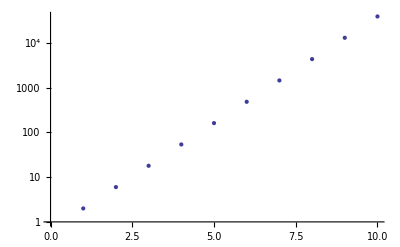

```mathematica
ListLogPlot[
Table[(3^n-3^(n-1)),{n,1,10}]
]
```

```mathematica
calc2=ReadList[FileNameForTupleBis[{3,31,43,173,229}]]
```

{«1»}

```mathematica
calc3=Take[GoodForTuple[{3,31,43,173,229}],5943]
```

{0,«5942»}

```mathematica
Length[calc2]
```

5943

```mathematica
Module[
{pos,calc2=ReadList[FileNameForTupleBis[{3,31,43,173,229}]],calc3=Take[GoodForTuple[{3,31,43,173,229}],5943]},
For[pos=1,pos<Length[calc3]-1,pos++,
If[calc2[[pos]]≠ calc3[[pos+1]],
Print[{calc2[[pos]], calc3[[pos+1]]}];
Break[]
]
]
]
```

{619936077624883545698997398859449791259575817655063735521634080436608973540529832537804126333470397809634646466801897806201836734788743382777517084078186751282776932470359234305521502440236092893569758603,1}

```mathematica
calc2[[1]]
```

619936077624883545698997398859449791259575817655063735521634080436608973540529832537804126333470397809634646466801897806201836734788743382777517084078186751282776932470359234305521502440236092893569758603

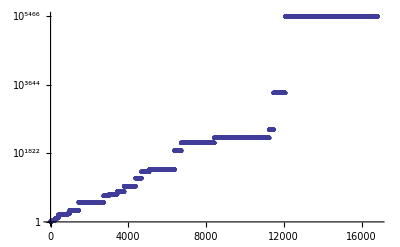

```mathematica
ListLogPlot[ReadList [FileNameForTupleBis[{3,31,43,173,229}]]]
```

```mathematica
N[Log[10,Last[ReadList[FileNameForTupleBis[{3,31,43,173,229}]]]]]*2
```

10931.8

```mathematica
DigitRatio[list_,digit_]:= Length[Select[list,#==digit&]]/Length[list]
```

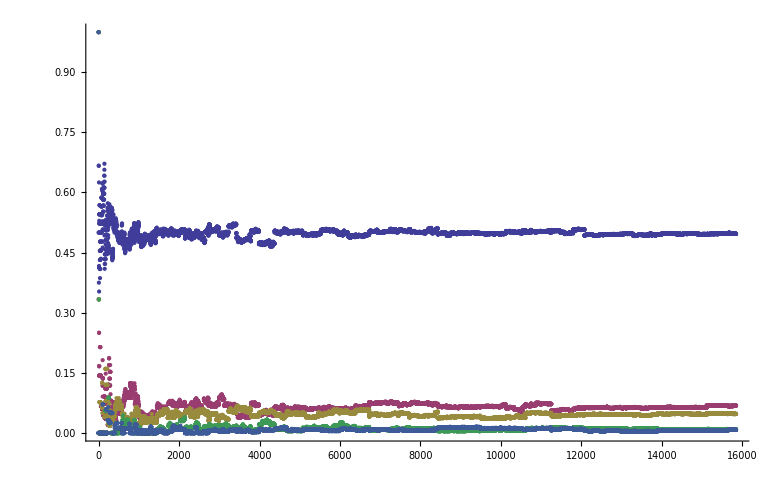

```mathematica
With[
{tuple={3,31,43,173,229}},
With[
{all=ReadList [FileNameForTupleBis[tuple]]},
ListPlot[
Table[
Table[
DigitRatio[IntegerDigits[v,p],1],{v,all}
],
{p,tuple}
]
]
]
]
```

```mathematica
DigitRatio[{1,2,3,1},1]
```

1/2

```mathematica
CalcGoodForTuple2[{3,5,7,11},2798309627212925596379312446328322623421420003045069452433799879263132097009146128125140482287689043052548418838108425431611226348989076735621530063174993819842873315871091884794805435456530534646064182596823524478218367284788945455651963488781070397727315221130160232426273550490119979996032042433473539205089142303465598290661712176144692048114641280211479003862546986449069179065077252245595266433714682848366638271724342101809561161732239220477623056835051224836944071736627798744532458250012542734836412757545916981305726260443622357998688376685162099332007288187691003979454263766559084563612999291075557886624093319621246853446311843734646040759816018134880439035129170074660196731445897200776701796592516038502331725031045716202357917387892372261097184740730744228857202116263120825022961428037934817162714805486925260989688233399549420053940722166581958099589587830220832166794184655903636690611725303425082073973195757524573962109880341093221978574150694781402995507925493701643857358866144932489068581014752198411238036658100717039373559391074859787779940525755008192179446702580160656105099290017856762333018215501796062734027328380279502157763705239678233618611830188720364577460109449553982269405065374440494408004898131589978879205841376173822019354814575475468100618141580372046216226096328425088469122676740003963662454012458380304422868004552689194824595399122293416247308723073124898538515414913205395523241053468061304677315990440658466726922053798588296730819665380379124929856997870211456879266950695302343446688758549109995120909303651963337111516428966403061105666877863147645422621736438170098503412641168360597652728906658739850893060095754081983446457735819659105699505678074403571366307630919731531214009005095191303608208177611081234513288164907215085470462287451655189796496270586616655624135119898301987900196987272994611514249860564848262688656554853103788688591151068684886532166597597976890691221242288748252080843311215711450146264569284689572711120439336873144968927840000025481215080474187583682243124472983410278098970452979145570074722792852685381767474230034804337327262975309620306502743167759612353138631576701221847446354741381375398858347095309169580149992351785151196335913578024004169402115422670747418360840673586074194990880299630064113794203901874371577404642398543052079488955361476363443347629168628687953600046402306364424975072233850066162451804869939810595288671578429656186410564671057818717474919200878671632994402120909651021118625255449071765213153745877749728934265179335525954532922617757897391683923242987225150007251,10^20000]
```

Aborted at value : 143420123643811061803742865423762445539716948951558373151521354935257579562207090099579828748701824863273938541887990781432601617907884682374574214151405987129869291609816443664328583693687692760846575132730160431423823922661136099084206450198883476898400380085293797078433113142895975949526546100576527957384116387201589877997864416556269484568047180368902098400966720790689764169132728097480356119180618706196224180044020384105139015042327837646994354465489828429190564094437400347303165344043119675848593669084185853877620613253744134794191397927336958339535137274109646875422361173792637139811953162672015840688904788255039328433400005004818829202518313817902853505978516743365760603253272644755530606922043122226830765821821442207604339300357201458652137029137254455726823610647551783529929401218998140638126137262125924435043434050740547130744680018397628518283592994080458289434261254472354987472245574944488058493724478939515615241573904767510756191772103204058353221084510463991971497166013675863900594795804504746232595969393983273396455284316532005186897064450045185547289873140043526412898514957303496675989919685038232413594892157726196980642661328478551105244410056009413073178272049846898805618087330604067837917088474535435951620836242918546234365103451810332797567073173882573446652448099925474995148837973929348069489912260825666499496925543569061670458708455538477807454849926409446191390319265866620418125048370670242273644645306502688054144196520272507022199308831683308304056544097971065886819885644971240747048216526096354044942913998843573590995161300728844148173686143175343119964303586352457962501959331199959756014279924893437897184817343305798109546909913396106224655317177314346099976422589788658550501974041531187949429440676055774917697006308230290356105189288113267937850016328425982912449877900017427259437734866973647778421057450663816105072098308879987510292669437900862198127265430135317639875784897261828437139122147007387324671129489047104517686412469346687794560643541941932417595385620505981797595150651463029729467927466194166030129035821031187923191685079992574764765083553783549162205160564546890801202310853552758481455924996012873927206578637343858594097907880712879398655957877900019700829368192435024396629159002726295044219859844989308894533204344797689055791831807692575246476963024568255573491821526657937579766671722833611270133580776591232316106803743042923669428476638232418914077205083503866661486439815049699144823141761419337157594725237818606409440726371074210111886074496741011479009080827570343635088200459796070498204000880126572485137648733589088567272721599944629740311789822474322144641925958956342321952273149379787944574290243137761329694345273636743615222460701668179275876308350340225069444777782681925796169827887240920962784169021445664914940362960030061271979756559479017289313229574900546669192668993349284466685047509901953156389097584633895569900401832610108778309475837601558561037259537780603025688375572782348106871118796344902446693177995824031792728939417151709426850182708739264668500389077845671800155116617047517794166062542585302759842707830194866304724159395421199718849800452531077329125919546959164757704890341274553370961511261221122194835881115794314064842245688780475684745401467965091562525201429453813288226346799685164600338265515686947099096776632145407289381712652394677095615903975282443491727960977134176503967438417826174785656391149700769800989907916365845611644359752396420383870909009175269572193510616536236040708453754734997687083803669021113953054942271888149907243013945808633523204858676012025375203692217484071152551769293154936920025349932276072362657001198516805960669895370074300444684922695159912109375

Aborted at value :